# Calculation of LLP particle flux due to cosmic rays --- Draft 1!

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Set constants

```mathematica
c = 3*10^8;(*m/s*)
Gf =1.16638*10^(-5); (*GeV^-2*)
```

## Cosmic ray flux

Import cosmic ray flux data from Abe, Koh, et al. “Measurements of cosmic-ray proton and helium spectra from the BESS-Polar long-duration balloon flights over Antarctica.” The Astrophysical Journal 822.2 (2016): 65.

```mathematica
binList = Import["CRKeyVals.csv"];
binList =Delete[binList,1];
energyBins = Table[{binList[[i,2]],binList[[i,4]]},{i,1,Length[binList]}];
energyWidth = Table[binList[[i+69,5]],{i,1,20}];
```

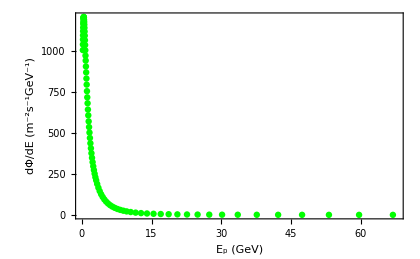

```mathematica
ListPlot[energyBins,FrameLabel->{"E_p (GeV)","dΦ/dE (m^-2s^-1GeV^-1)"},Frame->True,LabelStyle->{Black,15},ImageSize->420,PlotStyle->Directive[Green,Thick]]
```

```mathematica
energyBins
```

{{0.206,1004.75},{0.218,1039},{0.231,1069.15},{0.244,1094.75},{0.259,1120},{0.274,1142},{0.29,1164.15},{0.307,1176.45},{0.326,1193.45},{0.345,1200.85},{0.366,1204.5},{0.387,1207.05},{0.41,1206.05},{0.435,1202.45},{0.46,1188.8},{0.487,1176.15},{0.516,1160.3},{0.547,1140.55},{0.579,1118.05},{0.614,1092.75},{0.65,1064.95},{0.688,1035.8},{0.729,1003.7},{0.772,971.1},{0.818,940.8},{0.866,905.05},{0.918,868.9},{0.972,831.4},{1.03,794.3},{1.091,754.35},{1.156,716.65},{1.224,680.6},{1.297,642.2},{1.374,606.95},{1.455,570.05},{1.541,535.55},{1.632,501.95},{1.729,468.9},{1.831,436.6},{1.94,406},{2.054,376.05},{2.176,347.95},{2.305,321.6},{2.442,296.25},{2.587,273.25},{2.74,250.95},{2.902,229.5},{3.074,210.55},{3.289,188.5},{3.551,165.7},{3.834,144.8},{4.14,126},{4.471,109.3},{4.827,94.38},{5.212,81.165},{5.628,69.605},{6.077,59.325},{6.562,50.475},{7.085,42.82},{7.65,36.1},{8.26,30.495},{8.919,25.505},{9.631,21.305},{10.505,17.395},{11.565,13.775},{12.73,10.91},{14.01,8.5975},{15.42,6.7365},{16.97,5.2745},{18.675,4.13},{20.555,3.209},{22.625,2.497},{24.905,1.9275},{27.415,1.4995},{30.175,1.157},{33.55,0.87225},{37.645,0.6363},{42.24,0.4644},{47.395,0.3392},{53.175,0.2481},{59.665,0.1807},{66.945,0.1315},{75.11,0.09677},{84.28,0.07018},{94.565,0.05062},{106.8,0.037575},{121.4,0.02622},{138,0.01871},{156.8,0.013255}}

```mathematica
intEB=Interpolation[energyBins,InterpolationOrder->1]
```

InterpolatingFunction[…]

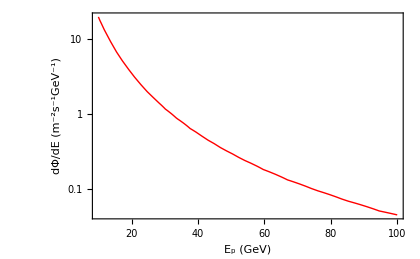

```mathematica
LogPlot[intEB[Ep],{Ep,10,100},FrameLabel->{"E_p (GeV)","dΦ/dE (m^-2s^-1GeV^-1)"},Frame->True,LabelStyle->{Black,15},ImageSize->420,PlotStyle->Directive[Red,Thick]]
```

## Pythia hadronization

First, we import the kaon results from our 10,000 event pythia runs.

```mathematica
For[i = 1, i <21, i++,  
If[i <10,
kaonPData[i]=Import[FileNameJoin[{NotebookDirectory[],"Data","ProtonScatter","kaonPData0" <>ToString[i]<>".txt"}],"table"];
kaonNData[i]=Import[FileNameJoin[{NotebookDirectory[],"Data","NeutronScatter","kaonNData0" <>ToString[i]<>".txt"}],"table"],kaonPData[i]=Import[FileNameJoin[{NotebookDirectory[],"Data","ProtonScatter","kaonPData" <>ToString[i]<>".txt"}],"table"];kaonNData[i]=Import[FileNameJoin[{NotebookDirectory[],"Data","NeutronScatter","kaonNData" <>ToString[i]<>".txt"}],"table"]
]

]
```

Test nested list element selection

```mathematica
kaonNData[1][[1]]
kaonNData[1][[1,3]]
kaonNData[1][[2]]
```

{Beams:eA,=,18.675}

18.675

{0,3.9598}

Calculate number of kaons produced for a given energy bin

```mathematica
For[i = 1, i <21, i++,  
numPKaons[i]=Times@@Dimensions[kaonPData[i]]-1;
numNKaons[i]=Times@@Dimensions[kaonNData[i]]-1;
numKaons[i] = numNKaons[i]+numPKaons[i]
]
```

```mathematica
numPKaons[1];
numNKaons[1];
numKaons[1];
```

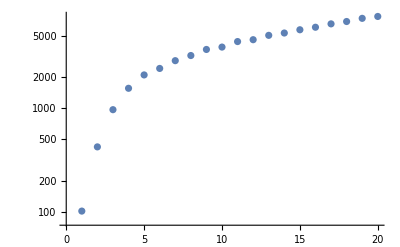

```mathematica
ListLogPlot[Table[numPKaons[i],{i,1,20}]]
```

Obtain a probability distribution of kaons over energy

### Tests

```mathematica
testkEngPoints=Table[kaonData[1][[j,2]],{j,2,numKaons[1]+1}]
```

Part::partw: Part 2 of kaonData[1] does not exist.

Part::partw: Part 3 of kaonData[1] does not exist.

Part::partw: Part 4 of kaonData[1] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{kaonData[1]⟦2,2⟧,kaonData[1]⟦3,2⟧,kaonData[1]⟦4,2⟧,kaonData[1]⟦5,2⟧,kaonData[1]⟦6,2⟧,kaonData[1]⟦7,2⟧,kaonData[1]⟦8,2⟧,kaonData[1]⟦9,2⟧,kaonData[1]⟦10,2⟧,kaonData[1]⟦11,2⟧,kaonData[1]⟦12,2⟧,kaonData[1]⟦13,2⟧,kaonData[1]⟦14,2⟧,kaonData[1]⟦15,2⟧,kaonData[1]⟦16,2⟧,kaonData[1]⟦17,2⟧,kaonData[1]⟦18,2⟧,kaonData[1]⟦19,2⟧,kaonData[1]⟦20,2⟧,kaonData[1]⟦21,2⟧,kaonData[1]⟦22,2⟧,kaonData[1]⟦23,2⟧,kaonData[1]⟦24,2⟧,kaonData[1]⟦25,2⟧,kaonData[1]⟦26,2⟧,kaonData[1]⟦27,2⟧,kaonData[1]⟦28,2⟧,kaonData[1]⟦29,2⟧,kaonData[1]⟦30,2⟧,kaonData[1]⟦31,2⟧,kaonData[1]⟦32,2⟧,kaonData[1]⟦33,2⟧,kaonData[1]⟦34,2⟧,kaonData[1]⟦35,2⟧,kaonData[1]⟦36,2⟧,kaonData[1]⟦37,2⟧,kaonData[1]⟦38,2⟧,kaonData[1]⟦39,2⟧,kaonData[1]⟦40,2⟧,kaonData[1]⟦41,2⟧,kaonData[1]⟦42,2⟧,kaonData[1]⟦43,2⟧,kaonData[1]⟦44,2⟧,kaonData[1]⟦45,2⟧,kaonData[1]⟦46,2⟧,kaonData[1]⟦47,2⟧,kaonData[1]⟦48,2⟧,kaonData[1]⟦49,2⟧,kaonData[1]⟦50,2⟧,kaonData[1]⟦51,2⟧,kaonData[1]⟦52,2⟧,kaonData[1]⟦53,2⟧,kaonData[1]⟦54,2⟧,kaonData[1]⟦55,2⟧,kaonData[1]⟦56,2⟧,kaonData[1]⟦57,2⟧,kaonData[1]⟦58,2⟧,kaonData[1]⟦59,2⟧,kaonData[1]⟦60,2⟧,kaonData[1]⟦61,2⟧,kaonData[1]⟦62,2⟧,kaonData[1]⟦63,2⟧,kaonData[1]⟦64,2⟧,kaonData[1]⟦65,2⟧,kaonData[1]⟦66,2⟧,kaonData[1]⟦67,2⟧,kaonData[1]⟦68,2⟧,kaonData[1]⟦69,2⟧,kaonData[1]⟦70,2⟧,kaonData[1]⟦71,2⟧,kaonData[1]⟦72,2⟧,kaonData[1]⟦73,2⟧,kaonData[1]⟦74,2⟧,kaonData[1]⟦75,2⟧,kaonData[1]⟦76,2⟧,kaonData[1]⟦77,2⟧,kaonData[1]⟦78,2⟧,kaonData[1]⟦79,2⟧,kaonData[1]⟦80,2⟧,kaonData[1]⟦81,2⟧,kaonData[1]⟦82,2⟧,kaonData[1]⟦83,2⟧,kaonData[1]⟦84,2⟧,kaonData[1]⟦85,2⟧,kaonData[1]⟦86,2⟧,kaonData[1]⟦87,2⟧,kaonData[1]⟦88,2⟧,kaonData[1]⟦89,2⟧,kaonData[1]⟦90,2⟧,kaonData[1]⟦91,2⟧,kaonData[1]⟦92,2⟧,kaonData[1]⟦93,2⟧,kaonData[1]⟦94,2⟧,kaonData[1]⟦95,2⟧,kaonData[1]⟦96,2⟧,kaonData[1]⟦97,2⟧,kaonData[1]⟦98,2⟧,kaonData[1]⟦99,2⟧,kaonData[1]⟦100,2⟧,kaonData[1]⟦101,2⟧,kaonData[1]⟦102,2⟧,kaonData[1]⟦103,2⟧,kaonData[1]⟦104,2⟧,kaonData[1]⟦105,2⟧,kaonData[1]⟦106,2⟧,kaonData[1]⟦107,2⟧,kaonData[1]⟦108,2⟧,kaonData[1]⟦109,2⟧,kaonData[1]⟦110,2⟧,kaonData[1]⟦111,2⟧,kaonData[1]⟦112,2⟧,kaonData[1]⟦113,2⟧,kaonData[1]⟦114,2⟧,kaonData[1]⟦115,2⟧,kaonData[1]⟦116,2⟧,kaonData[1]⟦117,2⟧,kaonData[1]⟦118,2⟧,kaonData[1]⟦119,2⟧,kaonData[1]⟦120,2⟧,kaonData[1]⟦121,2⟧,kaonData[1]⟦122,2⟧,kaonData[1]⟦123,2⟧,kaonData[1]⟦124,2⟧,kaonData[1]⟦125,2⟧,kaonData[1]⟦126,2⟧,kaonData[1]⟦127,2⟧,kaonData[1]⟦128,2⟧,kaonData[1]⟦129,2⟧,kaonData[1]⟦130,2⟧,kaonData[1]⟦131,2⟧,kaonData[1]⟦132,2⟧,kaonData[1]⟦133,2⟧,kaonData[1]⟦134,2⟧,kaonData[1]⟦135,2⟧,kaonData[1]⟦136,2⟧,kaonData[1]⟦137,2⟧,kaonData[1]⟦138,2⟧,kaonData[1]⟦139,2⟧,kaonData[1]⟦140,2⟧,kaonData[1]⟦141,2⟧,kaonData[1]⟦142,2⟧,kaonData[1]⟦143,2⟧,kaonData[1]⟦144,2⟧,kaonData[1]⟦145,2⟧,kaonData[1]⟦146,2⟧,kaonData[1]⟦147,2⟧,kaonData[1]⟦148,2⟧,kaonData[1]⟦149,2⟧,kaonData[1]⟦150,2⟧,kaonData[1]⟦151,2⟧,kaonData[1]⟦152,2⟧,kaonData[1]⟦153,2⟧,kaonData[1]⟦154,2⟧,kaonData[1]⟦155,2⟧,kaonData[1]⟦156,2⟧,kaonData[1]⟦157,2⟧,kaonData[1]⟦158,2⟧,kaonData[1]⟦159,2⟧,kaonData[1]⟦160,2⟧,kaonData[1]⟦161,2⟧,kaonData[1]⟦162,2⟧,kaonData[1]⟦163,2⟧,kaonData[1]⟦164,2⟧,kaonData[1]⟦165,2⟧,kaonData[1]⟦166,2⟧,kaonData[1]⟦167,2⟧,kaonData[1]⟦168,2⟧,kaonData[1]⟦169,2⟧,kaonData[1]⟦170,2⟧,kaonData[1]⟦171,2⟧,kaonData[1]⟦172,2⟧,kaonData[1]⟦173,2⟧,kaonData[1]⟦174,2⟧,kaonData[1]⟦175,2⟧,kaonData[1]⟦176,2⟧,kaonData[1]⟦177,2⟧,kaonData[1]⟦178,2⟧,kaonData[1]⟦179,2⟧,kaonData[1]⟦180,2⟧,kaonData[1]⟦181,2⟧,kaonData[1]⟦182,2⟧,kaonData[1]⟦183,2⟧,kaonData[1]⟦184,2⟧,kaonData[1]⟦185,2⟧,kaonData[1]⟦186,2⟧,kaonData[1]⟦187,2⟧,kaonData[1]⟦188,2⟧,kaonData[1]⟦189,2⟧,kaonData[1]⟦190,2⟧,kaonData[1]⟦191,2⟧,kaonData[1]⟦192,2⟧,kaonData[1]⟦193,2⟧,kaonData[1]⟦194,2⟧,kaonData[1]⟦195,2⟧,kaonData[1]⟦196,2⟧,kaonData[1]⟦197,2⟧,kaonData[1]⟦198,2⟧,kaonData[1]⟦199,2⟧,kaonData[1]⟦200,2⟧,kaonData[1]⟦201,2⟧,kaonData[1]⟦202,2⟧,kaonData[1]⟦203,2⟧,kaonData[1]⟦204,2⟧,kaonData[1]⟦205,2⟧,kaonData[1]⟦206,2⟧,kaonData[1]⟦207,2⟧,kaonData[1]⟦208,2⟧,kaonData[1]⟦209,2⟧,kaonData[1]⟦210,2⟧,kaonData[1]⟦211,2⟧,kaonData[1]⟦212,2⟧,kaonData[1]⟦213,2⟧}

```mathematica
testsmoothkEng =SmoothKernelDistribution[testkEngPoints]
testsmoothkEng2 =SmoothKernelDistribution[Flatten@testkEngPoints,0.5]
```

SmoothKernelDistribution::invldd: The input data SmoothKernelDistribution[{kaonData[1]⟦2,2⟧,kaonData[1]⟦3,2⟧,kaonData[1]⟦4,2⟧,kaonData[1]⟦5,2⟧,kaonData[1]⟦6,2⟧,kaonData[1]⟦7,2⟧,kaonData[1]⟦8,2⟧,kaonData[1]⟦9,2⟧,kaonData[1]⟦10,2⟧,kaonData[1]⟦11,2⟧,kaonData[1]⟦12,2⟧,kaonData[1]⟦13,2⟧,kaonData[1]⟦14,2⟧,kaonData[1]⟦15,2⟧,«23»,kaonData[1]⟦39,2⟧,kaonData[1]⟦40,2⟧,kaonData[1]⟦41,2⟧,kaonData[1]⟦42,2⟧,kaonData[1]⟦43,2⟧,kaonData[1]⟦44,2⟧,kaonData[1]⟦45,2⟧,kaonData[1]⟦46,2⟧,kaonData[1]⟦47,2⟧,kaonData[1]⟦48,2⟧,kaonData[1]⟦49,2⟧,kaonData[1]⟦50,2⟧,kaonData[1]⟦51,2⟧,«162»}] should be a vector or a matrix of real numbers or a valid TemporalData object.

SmoothKernelDistribution[{kaonData[1]⟦2,2⟧,kaonData[1]⟦3,2⟧,kaonData[1]⟦4,2⟧,kaonData[1]⟦5,2⟧,kaonData[1]⟦6,2⟧,kaonData[1]⟦7,2⟧,kaonData[1]⟦8,2⟧,kaonData[1]⟦9,2⟧,kaonData[1]⟦10,2⟧,kaonData[1]⟦11,2⟧,kaonData[1]⟦12,2⟧,kaonData[1]⟦13,2⟧,kaonData[1]⟦14,2⟧,kaonData[1]⟦15,2⟧,kaonData[1]⟦16,2⟧,kaonData[1]⟦17,2⟧,kaonData[1]⟦18,2⟧,kaonData[1]⟦19,2⟧,kaonData[1]⟦20,2⟧,kaonData[1]⟦21,2⟧,kaonData[1]⟦22,2⟧,kaonData[1]⟦23,2⟧,kaonData[1]⟦24,2⟧,kaonData[1]⟦25,2⟧,kaonData[1]⟦26,2⟧,kaonData[1]⟦27,2⟧,kaonData[1]⟦28,2⟧,kaonData[1]⟦29,2⟧,kaonData[1]⟦30,2⟧,kaonData[1]⟦31,2⟧,kaonData[1]⟦32,2⟧,kaonData[1]⟦33,2⟧,kaonData[1]⟦34,2⟧,kaonData[1]⟦35,2⟧,kaonData[1]⟦36,2⟧,kaonData[1]⟦37,2⟧,kaonData[1]⟦38,2⟧,kaonData[1]⟦39,2⟧,kaonData[1]⟦40,2⟧,kaonData[1]⟦41,2⟧,kaonData[1]⟦42,2⟧,kaonData[1]⟦43,2⟧,kaonData[1]⟦44,2⟧,kaonData[1]⟦45,2⟧,kaonData[1]⟦46,2⟧,kaonData[1]⟦47,2⟧,kaonData[1]⟦48,2⟧,kaonData[1]⟦49,2⟧,kaonData[1]⟦50,2⟧,kaonData[1]⟦51,2⟧,kaonData[1]⟦52,2⟧,kaonData[1]⟦53,2⟧,kaonData[1]⟦54,2⟧,kaonData[1]⟦55,2⟧,kaonData[1]⟦56,2⟧,kaonData[1]⟦57,2⟧,kaonData[1]⟦58,2⟧,kaonData[1]⟦59,2⟧,kaonData[1]⟦60,2⟧,kaonData[1]⟦61,2⟧,kaonData[1]⟦62,2⟧,kaonData[1]⟦63,2⟧,kaonData[1]⟦64,2⟧,kaonData[1]⟦65,2⟧,kaonData[1]⟦66,2⟧,kaonData[1]⟦67,2⟧,kaonData[1]⟦68,2⟧,kaonData[1]⟦69,2⟧,kaonData[1]⟦70,2⟧,kaonData[1]⟦71,2⟧,kaonData[1]⟦72,2⟧,kaonData[1]⟦73,2⟧,kaonData[1]⟦74,2⟧,kaonData[1]⟦75,2⟧,kaonData[1]⟦76,2⟧,kaonData[1]⟦77,2⟧,kaonData[1]⟦78,2⟧,kaonData[1]⟦79,2⟧,kaonData[1]⟦80,2⟧,kaonData[1]⟦81,2⟧,kaonData[1]⟦82,2⟧,kaonData[1]⟦83,2⟧,kaonData[1]⟦84,2⟧,kaonData[1]⟦85,2⟧,kaonData[1]⟦86,2⟧,kaonData[1]⟦87,2⟧,kaonData[1]⟦88,2⟧,kaonData[1]⟦89,2⟧,kaonData[1]⟦90,2⟧,kaonData[1]⟦91,2⟧,kaonData[1]⟦92,2⟧,kaonData[1]⟦93,2⟧,kaonData[1]⟦94,2⟧,kaonData[1]⟦95,2⟧,kaonData[1]⟦96,2⟧,kaonData[1]⟦97,2⟧,kaonData[1]⟦98,2⟧,kaonData[1]⟦99,2⟧,kaonData[1]⟦100,2⟧,kaonData[1]⟦101,2⟧,kaonData[1]⟦102,2⟧,kaonData[1]⟦103,2⟧,kaonData[1]⟦104,2⟧,kaonData[1]⟦105,2⟧,kaonData[1]⟦106,2⟧,kaonData[1]⟦107,2⟧,kaonData[1]⟦108,2⟧,kaonData[1]⟦109,2⟧,kaonData[1]⟦110,2⟧,kaonData[1]⟦111,2⟧,kaonData[1]⟦112,2⟧,kaonData[1]⟦113,2⟧,kaonData[1]⟦114,2⟧,kaonData[1]⟦115,2⟧,kaonData[1]⟦116,2⟧,kaonData[1]⟦117,2⟧,kaonData[1]⟦118,2⟧,kaonData[1]⟦119,2⟧,kaonData[1]⟦120,2⟧,kaonData[1]⟦121,2⟧,kaonData[1]⟦122,2⟧,kaonData[1]⟦123,2⟧,kaonData[1]⟦124,2⟧,kaonData[1]⟦125,2⟧,kaonData[1]⟦126,2⟧,kaonData[1]⟦127,2⟧,kaonData[1]⟦128,2⟧,kaonData[1]⟦129,2⟧,kaonData[1]⟦130,2⟧,kaonData[1]⟦131,2⟧,kaonData[1]⟦132,2⟧,kaonData[1]⟦133,2⟧,kaonData[1]⟦134,2⟧,kaonData[1]⟦135,2⟧,kaonData[1]⟦136,2⟧,kaonData[1]⟦137,2⟧,kaonData[1]⟦138,2⟧,kaonData[1]⟦139,2⟧,kaonData[1]⟦140,2⟧,kaonData[1]⟦141,2⟧,kaonData[1]⟦142,2⟧,kaonData[1]⟦143,2⟧,kaonData[1]⟦144,2⟧,kaonData[1]⟦145,2⟧,kaonData[1]⟦146,2⟧,kaonData[1]⟦147,2⟧,kaonData[1]⟦148,2⟧,kaonData[1]⟦149,2⟧,kaonData[1]⟦150,2⟧,kaonData[1]⟦151,2⟧,kaonData[1]⟦152,2⟧,kaonData[1]⟦153,2⟧,kaonData[1]⟦154,2⟧,kaonData[1]⟦155,2⟧,kaonData[1]⟦156,2⟧,kaonData[1]⟦157,2⟧,kaonData[1]⟦158,2⟧,kaonData[1]⟦159,2⟧,kaonData[1]⟦160,2⟧,kaonData[1]⟦161,2⟧,kaonData[1]⟦162,2⟧,kaonData[1]⟦163,2⟧,kaonData[1]⟦164,2⟧,kaonData[1]⟦165,2⟧,kaonData[1]⟦166,2⟧,kaonData[1]⟦167,2⟧,kaonData[1]⟦168,2⟧,kaonData[1]⟦169,2⟧,kaonData[1]⟦170,2⟧,kaonData[1]⟦171,2⟧,kaonData[1]⟦172,2⟧,kaonData[1]⟦173,2⟧,kaonData[1]⟦174,2⟧,kaonData[1]⟦175,2⟧,kaonData[1]⟦176,2⟧,kaonData[1]⟦177,2⟧,kaonData[1]⟦178,2⟧,kaonData[1]⟦179,2⟧,kaonData[1]⟦180,2⟧,kaonData[1]⟦181,2⟧,kaonData[1]⟦182,2⟧,kaonData[1]⟦183,2⟧,kaonData[1]⟦184,2⟧,kaonData[1]⟦185,2⟧,kaonData[1]⟦186,2⟧,kaonData[1]⟦187,2⟧,kaonData[1]⟦188,2⟧,kaonData[1]⟦189,2⟧,kaonData[1]⟦190,2⟧,kaonData[1]⟦191,2⟧,kaonData[1]⟦192,2⟧,kaonData[1]⟦193,2⟧,kaonData[1]⟦194,2⟧,kaonData[1]⟦195,2⟧,kaonData[1]⟦196,2⟧,kaonData[1]⟦197,2⟧,kaonData[1]⟦198,2⟧,kaonData[1]⟦199,2⟧,kaonData[1]⟦200,2⟧,kaonData[1]⟦201,2⟧,kaonData[1]⟦202,2⟧,kaonData[1]⟦203,2⟧,kaonData[1]⟦204,2⟧,kaonData[1]⟦205,2⟧,kaonData[1]⟦206,2⟧,kaonData[1]⟦207,2⟧,kaonData[1]⟦208,2⟧,kaonData[1]⟦209,2⟧,kaonData[1]⟦210,2⟧,kaonData[1]⟦211,2⟧,kaonData[1]⟦212,2⟧,kaonData[1]⟦213,2⟧}]

SmoothKernelDistribution::invldd: The input data SmoothKernelDistribution[{kaonData[1]⟦2,2⟧,kaonData[1]⟦3,2⟧,kaonData[1]⟦4,2⟧,kaonData[1]⟦5,2⟧,kaonData[1]⟦6,2⟧,kaonData[1]⟦7,2⟧,kaonData[1]⟦8,2⟧,kaonData[1]⟦9,2⟧,kaonData[1]⟦10,2⟧,kaonData[1]⟦11,2⟧,kaonData[1]⟦12,2⟧,kaonData[1]⟦13,2⟧,kaonData[1]⟦14,2⟧,kaonData[1]⟦15,2⟧,«23»,kaonData[1]⟦39,2⟧,kaonData[1]⟦40,2⟧,kaonData[1]⟦41,2⟧,kaonData[1]⟦42,2⟧,kaonData[1]⟦43,2⟧,kaonData[1]⟦44,2⟧,kaonData[1]⟦45,2⟧,kaonData[1]⟦46,2⟧,kaonData[1]⟦47,2⟧,kaonData[1]⟦48,2⟧,kaonData[1]⟦49,2⟧,kaonData[1]⟦50,2⟧,kaonData[1]⟦51,2⟧,«162»}] should be a vector or a matrix of real numbers or a valid TemporalData object.

SmoothKernelDistribution[{kaonData[1]⟦2,2⟧,kaonData[1]⟦3,2⟧,kaonData[1]⟦4,2⟧,kaonData[1]⟦5,2⟧,kaonData[1]⟦6,2⟧,kaonData[1]⟦7,2⟧,kaonData[1]⟦8,2⟧,kaonData[1]⟦9,2⟧,kaonData[1]⟦10,2⟧,kaonData[1]⟦11,2⟧,kaonData[1]⟦12,2⟧,kaonData[1]⟦13,2⟧,kaonData[1]⟦14,2⟧,kaonData[1]⟦15,2⟧,kaonData[1]⟦16,2⟧,kaonData[1]⟦17,2⟧,kaonData[1]⟦18,2⟧,kaonData[1]⟦19,2⟧,kaonData[1]⟦20,2⟧,kaonData[1]⟦21,2⟧,kaonData[1]⟦22,2⟧,kaonData[1]⟦23,2⟧,kaonData[1]⟦24,2⟧,kaonData[1]⟦25,2⟧,kaonData[1]⟦26,2⟧,kaonData[1]⟦27,2⟧,kaonData[1]⟦28,2⟧,kaonData[1]⟦29,2⟧,kaonData[1]⟦30,2⟧,kaonData[1]⟦31,2⟧,kaonData[1]⟦32,2⟧,kaonData[1]⟦33,2⟧,kaonData[1]⟦34,2⟧,kaonData[1]⟦35,2⟧,kaonData[1]⟦36,2⟧,kaonData[1]⟦37,2⟧,kaonData[1]⟦38,2⟧,kaonData[1]⟦39,2⟧,kaonData[1]⟦40,2⟧,kaonData[1]⟦41,2⟧,kaonData[1]⟦42,2⟧,kaonData[1]⟦43,2⟧,kaonData[1]⟦44,2⟧,kaonData[1]⟦45,2⟧,kaonData[1]⟦46,2⟧,kaonData[1]⟦47,2⟧,kaonData[1]⟦48,2⟧,kaonData[1]⟦49,2⟧,kaonData[1]⟦50,2⟧,kaonData[1]⟦51,2⟧,kaonData[1]⟦52,2⟧,kaonData[1]⟦53,2⟧,kaonData[1]⟦54,2⟧,kaonData[1]⟦55,2⟧,kaonData[1]⟦56,2⟧,kaonData[1]⟦57,2⟧,kaonData[1]⟦58,2⟧,kaonData[1]⟦59,2⟧,kaonData[1]⟦60,2⟧,kaonData[1]⟦61,2⟧,kaonData[1]⟦62,2⟧,kaonData[1]⟦63,2⟧,kaonData[1]⟦64,2⟧,kaonData[1]⟦65,2⟧,kaonData[1]⟦66,2⟧,kaonData[1]⟦67,2⟧,kaonData[1]⟦68,2⟧,kaonData[1]⟦69,2⟧,kaonData[1]⟦70,2⟧,kaonData[1]⟦71,2⟧,kaonData[1]⟦72,2⟧,kaonData[1]⟦73,2⟧,kaonData[1]⟦74,2⟧,kaonData[1]⟦75,2⟧,kaonData[1]⟦76,2⟧,kaonData[1]⟦77,2⟧,kaonData[1]⟦78,2⟧,kaonData[1]⟦79,2⟧,kaonData[1]⟦80,2⟧,kaonData[1]⟦81,2⟧,kaonData[1]⟦82,2⟧,kaonData[1]⟦83,2⟧,kaonData[1]⟦84,2⟧,kaonData[1]⟦85,2⟧,kaonData[1]⟦86,2⟧,kaonData[1]⟦87,2⟧,kaonData[1]⟦88,2⟧,kaonData[1]⟦89,2⟧,kaonData[1]⟦90,2⟧,kaonData[1]⟦91,2⟧,kaonData[1]⟦92,2⟧,kaonData[1]⟦93,2⟧,kaonData[1]⟦94,2⟧,kaonData[1]⟦95,2⟧,kaonData[1]⟦96,2⟧,kaonData[1]⟦97,2⟧,kaonData[1]⟦98,2⟧,kaonData[1]⟦99,2⟧,kaonData[1]⟦100,2⟧,kaonData[1]⟦101,2⟧,kaonData[1]⟦102,2⟧,kaonData[1]⟦103,2⟧,kaonData[1]⟦104,2⟧,kaonData[1]⟦105,2⟧,kaonData[1]⟦106,2⟧,kaonData[1]⟦107,2⟧,kaonData[1]⟦108,2⟧,kaonData[1]⟦109,2⟧,kaonData[1]⟦110,2⟧,kaonData[1]⟦111,2⟧,kaonData[1]⟦112,2⟧,kaonData[1]⟦113,2⟧,kaonData[1]⟦114,2⟧,kaonData[1]⟦115,2⟧,kaonData[1]⟦116,2⟧,kaonData[1]⟦117,2⟧,kaonData[1]⟦118,2⟧,kaonData[1]⟦119,2⟧,kaonData[1]⟦120,2⟧,kaonData[1]⟦121,2⟧,kaonData[1]⟦122,2⟧,kaonData[1]⟦123,2⟧,kaonData[1]⟦124,2⟧,kaonData[1]⟦125,2⟧,kaonData[1]⟦126,2⟧,kaonData[1]⟦127,2⟧,kaonData[1]⟦128,2⟧,kaonData[1]⟦129,2⟧,kaonData[1]⟦130,2⟧,kaonData[1]⟦131,2⟧,kaonData[1]⟦132,2⟧,kaonData[1]⟦133,2⟧,kaonData[1]⟦134,2⟧,kaonData[1]⟦135,2⟧,kaonData[1]⟦136,2⟧,kaonData[1]⟦137,2⟧,kaonData[1]⟦138,2⟧,kaonData[1]⟦139,2⟧,kaonData[1]⟦140,2⟧,kaonData[1]⟦141,2⟧,kaonData[1]⟦142,2⟧,kaonData[1]⟦143,2⟧,kaonData[1]⟦144,2⟧,kaonData[1]⟦145,2⟧,kaonData[1]⟦146,2⟧,kaonData[1]⟦147,2⟧,kaonData[1]⟦148,2⟧,kaonData[1]⟦149,2⟧,kaonData[1]⟦150,2⟧,kaonData[1]⟦151,2⟧,kaonData[1]⟦152,2⟧,kaonData[1]⟦153,2⟧,kaonData[1]⟦154,2⟧,kaonData[1]⟦155,2⟧,kaonData[1]⟦156,2⟧,kaonData[1]⟦157,2⟧,kaonData[1]⟦158,2⟧,kaonData[1]⟦159,2⟧,kaonData[1]⟦160,2⟧,kaonData[1]⟦161,2⟧,kaonData[1]⟦162,2⟧,kaonData[1]⟦163,2⟧,kaonData[1]⟦164,2⟧,kaonData[1]⟦165,2⟧,kaonData[1]⟦166,2⟧,kaonData[1]⟦167,2⟧,kaonData[1]⟦168,2⟧,kaonData[1]⟦169,2⟧,kaonData[1]⟦170,2⟧,kaonData[1]⟦171,2⟧,kaonData[1]⟦172,2⟧,kaonData[1]⟦173,2⟧,kaonData[1]⟦174,2⟧,kaonData[1]⟦175,2⟧,kaonData[1]⟦176,2⟧,kaonData[1]⟦177,2⟧,kaonData[1]⟦178,2⟧,kaonData[1]⟦179,2⟧,kaonData[1]⟦180,2⟧,kaonData[1]⟦181,2⟧,kaonData[1]⟦182,2⟧,kaonData[1]⟦183,2⟧,kaonData[1]⟦184,2⟧,kaonData[1]⟦185,2⟧,kaonData[1]⟦186,2⟧,kaonData[1]⟦187,2⟧,kaonData[1]⟦188,2⟧,kaonData[1]⟦189,2⟧,kaonData[1]⟦190,2⟧,kaonData[1]⟦191,2⟧,kaonData[1]⟦192,2⟧,kaonData[1]⟦193,2⟧,kaonData[1]⟦194,2⟧,kaonData[1]⟦195,2⟧,kaonData[1]⟦196,2⟧,kaonData[1]⟦197,2⟧,kaonData[1]⟦198,2⟧,kaonData[1]⟦199,2⟧,kaonData[1]⟦200,2⟧,kaonData[1]⟦201,2⟧,kaonData[1]⟦202,2⟧,kaonData[1]⟦203,2⟧,kaonData[1]⟦204,2⟧,kaonData[1]⟦205,2⟧,kaonData[1]⟦206,2⟧,kaonData[1]⟦207,2⟧,kaonData[1]⟦208,2⟧,kaonData[1]⟦209,2⟧,kaonData[1]⟦210,2⟧,kaonData[1]⟦211,2⟧,kaonData[1]⟦212,2⟧,kaonData[1]⟦213,2⟧},0.5]

```mathematica
Table[Plot[f[testsmoothkEng,x],{x,0,10},PlotLabel->f],{f,{PDF,CDF}}]
Table[Plot[f[testsmoothkEng2,x],{x,0,10},PlotLabel->f],{f,{PDF,CDF}}]
```

Part::partw: Part 2 of kaonData[1.] does not exist.

Part::partw: Part 3 of kaonData[1.] does not exist.

Part::partw: Part 4 of kaonData[1.] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

SmoothKernelDistribution::invldd: The input data SmoothKernelDistribution[{kaonData[1.]⟦2,2⟧,kaonData[1.]⟦3,2⟧,kaonData[1.]⟦4,2⟧,kaonData[1.]⟦5,2⟧,kaonData[1.]⟦6,2⟧,kaonData[1.]⟦7,2⟧,kaonData[1.]⟦8,2⟧,kaonData[1.]⟦9,2⟧,kaonData[1.]⟦10,2⟧,kaonData[1.]⟦11,2⟧,kaonData[1.]⟦12,2⟧,kaonData[1.]⟦13,2⟧,kaonData[1.]⟦14,2⟧,«26»,kaonData[1.]⟦41,2⟧,kaonData[1.]⟦42,2⟧,kaonData[1.]⟦43,2⟧,kaonData[1.]⟦44,2⟧,kaonData[1.]⟦45,2⟧,kaonData[1.]⟦46,2⟧,kaonData[1.]⟦47,2⟧,kaonData[1.]⟦48,2⟧,kaonData[1.]⟦49,2⟧,kaonData[1.]⟦50,2⟧,kaonData[1.]⟦51,2⟧,«162»}] should be a vector or a matrix of real numbers or a valid TemporalData object.

General::stop: Further output of SmoothKernelDistribution::invldd will be suppressed during this calculation.

{-Graphics-,-Graphics-}

Part::partw: Part 2 of kaonData[1.] does not exist.

Part::partw: Part 3 of kaonData[1.] does not exist.

Part::partw: Part 4 of kaonData[1.] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

SmoothKernelDistribution::invldd: The input data SmoothKernelDistribution[{kaonData[1.]⟦2,2⟧,kaonData[1.]⟦3,2⟧,kaonData[1.]⟦4,2⟧,kaonData[1.]⟦5,2⟧,kaonData[1.]⟦6,2⟧,kaonData[1.]⟦7,2⟧,kaonData[1.]⟦8,2⟧,kaonData[1.]⟦9,2⟧,kaonData[1.]⟦10,2⟧,kaonData[1.]⟦11,2⟧,kaonData[1.]⟦12,2⟧,kaonData[1.]⟦13,2⟧,kaonData[1.]⟦14,2⟧,«26»,kaonData[1.]⟦41,2⟧,kaonData[1.]⟦42,2⟧,kaonData[1.]⟦43,2⟧,kaonData[1.]⟦44,2⟧,kaonData[1.]⟦45,2⟧,kaonData[1.]⟦46,2⟧,kaonData[1.]⟦47,2⟧,kaonData[1.]⟦48,2⟧,kaonData[1.]⟦49,2⟧,kaonData[1.]⟦50,2⟧,kaonData[1.]⟦51,2⟧,«162»}] should be a vector or a matrix of real numbers or a valid TemporalData object.

General::stop: Further output of SmoothKernelDistribution::invldd will be suppressed during this calculation.

{-Graphics-,-Graphics-}

```mathematica
testTrunkEng =TruncatedDistribution[{0,1000},testsmoothkEng];
testTrunkEng2 =TruncatedDistribution[{0,1000},testsmoothkEng2];
```

```mathematica
Plot[PDF[testTrunkEng,x],{x,0,10}]
```

Part::partw: Part 2 of kaonData[1.] does not exist.

Part::partw: Part 3 of kaonData[1.] does not exist.

Part::partw: Part 4 of kaonData[1.] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

SmoothKernelDistribution::invldd: The input data SmoothKernelDistribution[{kaonData[1.]⟦2,2⟧,kaonData[1.]⟦3,2⟧,kaonData[1.]⟦4,2⟧,kaonData[1.]⟦5,2⟧,kaonData[1.]⟦6,2⟧,kaonData[1.]⟦7,2⟧,kaonData[1.]⟦8,2⟧,kaonData[1.]⟦9,2⟧,kaonData[1.]⟦10,2⟧,kaonData[1.]⟦11,2⟧,kaonData[1.]⟦12,2⟧,kaonData[1.]⟦13,2⟧,kaonData[1.]⟦14,2⟧,«26»,kaonData[1.]⟦41,2⟧,kaonData[1.]⟦42,2⟧,kaonData[1.]⟦43,2⟧,kaonData[1.]⟦44,2⟧,kaonData[1.]⟦45,2⟧,kaonData[1.]⟦46,2⟧,kaonData[1.]⟦47,2⟧,kaonData[1.]⟦48,2⟧,kaonData[1.]⟦49,2⟧,kaonData[1.]⟦50,2⟧,kaonData[1.]⟦51,2⟧,«162»}] should be a vector or a matrix of real numbers or a valid TemporalData object.

General::stop: Further output of SmoothKernelDistribution::invldd will be suppressed during this calculation.

-Graphics-

### PDF Calculations

```mathematica
For[i = 1, i <21, i++,  
kEngPointsP=Table[kaonPData[i][[j,2]],{j,2,numPKaons[i]+1}];
smoothkEngP =SmoothKernelDistribution[kEngPointsP];
smoothkEng2P =SmoothKernelDistribution[Flatten@kEngPointsP,0.5];
trunkEngP[i] =TruncatedDistribution[{0,1000},smoothkEngP];
trunkEng2P[i] =TruncatedDistribution[{0,1000},smoothkEng2P];
]
```

```mathematica
For[i = 1, i <21, i++,  
kEngPointsN=Table[kaonNData[i][[j,2]],{j,2,numNKaons[i]+1}];
smoothkEngN =SmoothKernelDistribution[kEngPointsN];
smoothkEng2N =SmoothKernelDistribution[Flatten@kEngPointsN,0.5];
trunkEngN[i] =TruncatedDistribution[{0,1000},smoothkEngN];
trunkEng2N[i] =TruncatedDistribution[{0,1000},smoothkEng2N];
]
```

```mathematica
For[i = 1, i <21, i++,  
kEngPoints=Join[Table[kaonNData[i][[j,2]],{j,2,numNKaons[i]+1}],Table[kaonPData[i][[j,2]],{j,2,numPKaons[i]+1}]];
smoothkEng =SmoothKernelDistribution[kEngPoints];
smoothkEng2 =SmoothKernelDistribution[Flatten@kEngPoints,0.5];
trunkEng[i] =TruncatedDistribution[{0,1000},smoothkEng];
trunkEng2[i] =TruncatedDistribution[{0,1000},smoothkEng2];
]
```

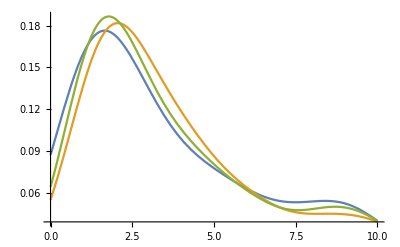

```mathematica
Plot[{PDF[trunkEngP[1],x],PDF[trunkEngN[1],x],PDF[trunkEng[1],x]},{x,0,10}]
```

## LLP flux calculation

The overall form of this expression is: kaon energy distribution X kaons produced per proton X proton flux in a given energy bin

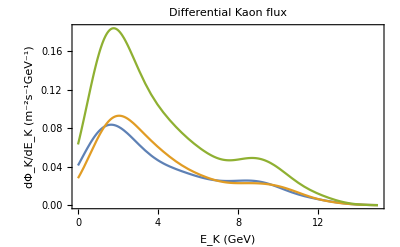

```mathematica
Plot[{4Pi*Evaluate[PDF[trunkEngP[1],x]]*numPKaons[1]/(2*10^4)*( intEB[
kaonPData[1][[1,3]]]* energyWidth[[1]]),4Pi*Evaluate[PDF[trunkEngN[1],x]]*numNKaons[1]/(2*10^4)*( intEB[
kaonNData[1][[1,3]]]* energyWidth[[1]]),4Pi*Evaluate[PDF[trunkEng[1],x]]*numKaons[1]/(2*10^4)*( intEB[
kaonPData[1][[1,3]]]* energyWidth[[1]])},{x,0,15},Frame->True,FrameLabel->{"E_K (GeV)","dΦ_K/dE_K (m^-2s^-1GeV^-1)"},PlotLabel->"Differential Kaon flux"]
```

1st line is just one low energy (18 GeV) trial bin, the 2nd is all protons under 30 GeV, the 3rd is all under 50 GeV, the 4th is under 100 GeV, and the final is all energies that the data I’m using has information for.

```mathematica
dKFlux18GeV=4Pi*Evaluate[PDF[trunkEng[1],x]]*numKaons[1]/(2*10^4)*( intEB[
kaonPData[1][[1,3]]]* energyWidth[[1]]);
dKFluxSub30=4Pi*Sum[Evaluate[PDF[trunkEng[i],x]]*numKaons[i]/(2*10^4)*( intEB[
kaonPData[i][[1,3]]]* energyWidth[[i]]),{i,1,5}];
dKFluxSub50 = 4Pi*Sum[Evaluate[PDF[trunkEng[i],x]]*numKaons[i]/(2*10^4)*( intEB[
kaonPData[i][[1,3]]]* energyWidth[[i]]),{i,1,10}];
dKFluxSub100 =4Pi*Sum[Evaluate[PDF[trunkEng[i],x]]*numKaons[i]/(2*10^4)*( intEB[
kaonPData[i][[1,3]]]* energyWidth[[i]]),{i,1,16}];
dKFluxAll =4Pi*Sum[Evaluate[PDF[trunkEng[i],x]]*numKaons[i]/(2*10^4)*( intEB[
kaonPData[i][[1,3]]]* energyWidth[[i]]),{i,1,20}];
```

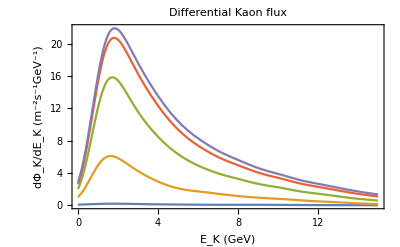

```mathematica
Plot[{dKFlux18GeV,dKFluxSub30,dKFluxSub50,dKFluxSub100,dKFluxAll},{x,0,15},Frame->True,FrameLabel->{"E_K (GeV)","dΦ_K/dE_K (m^-2s^-1GeV^-1)"},PlotLabel->"Differential Kaon flux"]
```

## Geometry

Here, I introduce all the equations required for the geometry calculations including detector parameters.

```mathematica
L[θ_,R_,h_]:=R*Cos[θ]+Sqrt[h^2 + 2R*h+R^2 *Cos[θ]^2](*In km*)
G[R_,h_]:=N[Integrate[Evaluate[Sin[θ]*((R+h)/L[θ,R,h])(1+((R*Cos[θ])/(L[θ,R,h]-R*Cos[θ])))],{θ,0,Pi}]]
```

```mathematica
volSK=Pi*(14.9)^2*32.2; (*In m^3*)
volHK=8*volSK;
```

```mathematica
detectionTime = 365.25*10*24*3600; (*In s, assuming 10 year detection period*)
```

```mathematica
Gmod[R_,h_,phiEng_,mPhi_]:=NIntegrate[Evaluate[Sin[θ]*((R+h)/L[θ,R,h])(1+((R*Cos[θ])/(L[θ,R,h]-R*Cos[θ])))*Exp[-(L[θ,R,h]*1000)/disTravel[phiEng,mPhi]]],{θ,0,Pi}](*This includes the exponential part of the number of events integral*)
```

```mathematica
pointList = Import["llpLifetimePoints.csv"];
pointTable = Table[{pointList[[i,1]],pointList[[i,2]]},{i,1,Length[pointList]}];
intLT = Interpolation[pointTable,InterpolationOrder->1]
```

InterpolatingFunction[…]

## Maybe Run

## Scalar Kinematics

```mathematica
pPhiCM[mPhi_] :=Sqrt[(mKaon^2 -(mPi + mPhi)^2)(mKaon^2 -(mPi - mPhi)^2)]/(2*mKaon);
ePhiCM[mPhi_] := Sqrt[pPhiCM[mPhi]^2 + mPhi^2];
ePhi[mPhi_,eK_,ctheta_] :=(eK/mKaon)(ePhiCM[mPhi]+pPhiCM[mPhi]Sqrt[1 - (mKaon^2)/(eK^2)]ctheta) ;
```

```mathematica
mKaon = 0.4937 ;(*In GeV*)
mPi = 0.1396 ;(*In GeV*)
me =0.000511;
ms=0.101;
mt=173;
md = 0.005;
CKMfactor = 3.07*10^(-4);
tauK = 1.24*10^(-8)*(1.5192675*10^(24));
```

Set ϕ mass and other inputs:

```mathematica
minEng = 1;(*GeV*)
step=0.15; (*GeV*)
mPhi = 0.150; (*In GeV*)
If[mPhi ≤ 0.2,tauPhiPlot = 10^(-1.116*Log[10,mPhi]+0.4777), tauPhiPlot = intLT[mPhi]];(*In s, from scalar spectator plot*)
mixingAngle = 10^(-3);
tauPhi = tauPhiPlot(10^(-6)/mixingAngle)^2;
minPhiEng = 0.05+ mPhi; (*Adjust these for final integral over Ephi: must be larger than mPhi*)
engStep = 0.1;
```

Calculate ϕ branching ratio:

```mathematica
Fkpi = ((mKaon^2 -mPi^2)/(ms -md))*fkpi;
fkpi =0.96(1+0.02(mPhi^2)/mPi^2);
```

```mathematica
phiBR = 9*Sqrt[2]*tauK*mixingAngle^2 *Gf^3*mt^4*ms^2*CKMfactor^2*Fkpi^2pPhiCM[mPhi]/(512*Pi^5*mKaon^2)(*BR to scalar, from Arxiv:1312.2547. Note that I pulled in a 1/2mk into the pPhiCM*)
phiBR2 =Sin[mixingAngle]^2 *0.002*2pPhiCM[mPhi]/mKaon (*from Arxiv:1310.8042*)
phiBR3 = 1; (*Used to construct the plot for seeing the energy distribution of both kaons and phis*)
```

9.02715×10^-9

1.61941×10^-9

Define kinematic functions:

```mathematica
gamma[phiEng_,mPhi_] :=phiEng/mPhi (*phiEng in GeV*)
velPhi[phiEng_,mPhi_] := Sqrt[1-(1/gamma[phiEng,mPhi]^2 )]*c(*outputs m/s^2*)
disTravel[phiEng_,mPhi_]:=gamma[phiEng,mPhi]*velPhi[phiEng,mPhi]*tauPhi;(*output in m*)
```

Generate theta distribution

```mathematica
costhetaData =RandomVariate[UniformDistribution[{-1, 1}],10^5];
```

#### Tests

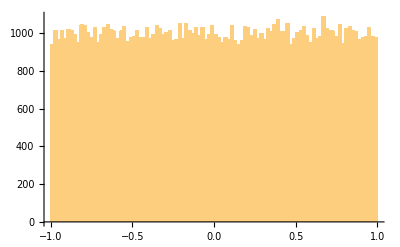

```mathematica
Histogram[costhetaData,100]
```

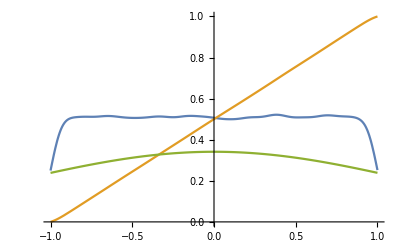

```mathematica
testKern = TruncatedDistribution[{-1,1},SmoothKernelDistribution[costhetaData]];
testKern2 = SmoothKernelDistribution[costhetaData,0.1];
testKern3 = SmoothKernelDistribution[costhetaData,1];
Plot[{PDF[testKern,x],CDF[testKern,x],PDF[testKern3,x]},{x,-1,1},PlotRange -> {{-1,1},{0,1}}]
```

```mathematica
eK = 1; (*GeV*)
```

```mathematica
(* ePhiDist=SmoothKernelDistribution[(eK/mKaon)(ePhiCM[mPhi]+pPhiCM[mPhi]Sqrt[1 - (mKaon^2)/(eK^2)]costhetaData)] ;*)
ePhiDist = UniformDistribution[{(eK/mKaon)(ePhiCM[mPhi]-pPhiCM[mPhi]Sqrt[1 - (mKaon^2)/(eK^2)]),(eK/mKaon)(ePhiCM[mPhi]+pPhiCM[mPhi]Sqrt[1 - (mKaon^2)/(eK^2)])}];
```

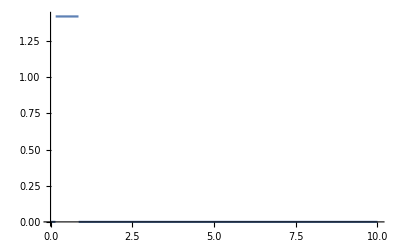

```mathematica
Plot[PDF[ePhiDist,x],{x,0,10}]
```

#### Create total probability distribution

```mathematica
For[s = 1, s< (15/step), s++,
eK =minEng + (s-1)(step);
ePhiDist= UniformDistribution[{(eK/mKaon)(ePhiCM[mPhi]-pPhiCM[mPhi]Sqrt[1 - (mKaon^2)/(eK^2)]),(eK/mKaon)(ePhiCM[mPhi]+pPhiCM[mPhi]Sqrt[1 - (mKaon^2)/(eK^2)])}];
truncEPhi[s] =TruncatedDistribution[{0,1000},ePhiDist];
]
```

```mathematica
For[s = 1, s< (15/step), s++,
eK =minEng + (s-1)(step);
x =minEng + (s-1)(step);
If[s == 1,totDist = truncEPhi[s],
t = 1;
fluxBelow = 0;
While[t< s,
x=minEng + (t-1)(step);
fluxBelow += dKFluxAll;
t++;
];
x=minEng + (s-1)(step);
fluxAt =dKFluxAll;
totDist=MixtureDistribution[{fluxBelow,fluxAt},{totDist,truncEPhi[s]}]  ]
]
```

```mathematica
totFlux = 0;
For[s = 1, s< (15/step), s++,
x =minEng + (s-1)(step);
totFlux +=dKFluxAll*step;
]
totFlux
```

114.337

### Distribution data

Flag whether or not to get dist data. (Slows down notebook a lot)

```mathematica
getDistData =0;
```

```mathematica
If[getdistData ==1, For[t = 1, t< 1000, t++,
y = minEng + t*(15-minEng)/1000;
distData[t] = PDF[totDist,y];
If[Mod[t,10]==0,Print[t]]
]];
```

```mathematica
dPhiFlux=Evaluate[PDF[totDist,x]]*totFlux*phiBR;
```

```mathematica
distData[3]
```

distData[3]

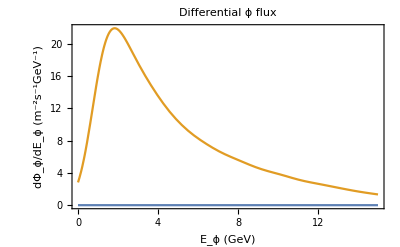

```mathematica
Plot[{phiBR*PDF[totDist,x]*totFlux,dKFluxAll},{x,0,15},Frame->True,FrameLabel->{"E_ϕ (GeV)","dΦ_ϕ/dE_ϕ (m^-2s^-1GeV^-1)"},PlotLabel->"Differential ϕ flux"]
```

```mathematica
phiBins = Table[{N[minEng + i*(15-minEng)/100],distData[i*10]},{i,1,100}];
```

```mathematica
intPhi=Interpolation[phiBins,InterpolationOrder->5]
```

InterpolatingFunction[…]

```mathematica
Plot[intPhi[Ep],{Ep,1,15},FrameLabel->{"E_phi (GeV)","dΦ/dE (m^-2s^-1GeV^-1)"},Frame->True,LabelStyle->{Black,15},ImageSize->420,PlotStyle->Directive[Red,Thick]]
```

InterpolatingFunction::dmval: Input value {1.00029} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
dPhiFluxSmooth =phiBR*totFlux*InterpolatingFunction[…];
```

```mathematica
dPhiFluxSmooth[3]
```

(1.03214×10^-6 InterpolatingFunction[…])[3]

InterpolatingFunction::dmval: Input value {0.000306429} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.306429} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.612551} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

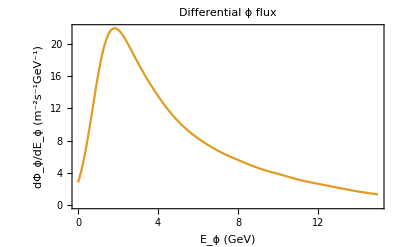

```mathematica
Plot[{phiBR*totFlux*intPhi[x],dKFluxAll},{x,0,15},Frame->True,FrameLabel->{"E_ϕ (GeV)","dΦ_ϕ/dE_ϕ (m^-2s^-1GeV^-1)"},PlotLabel->"Differential ϕ flux"]
```

## Number of Events

```mathematica
NumberOfEvents=Floor[volHK*detectionTime*Sum[engStep*Gmod[6400,10,minPhiEng + i*engStep,mPhi]*phiBR*PDF[totDist,minPhiEng+i*engStep]*totFlux/disTravel[minPhiEng+i*engStep,mPhi],{i,1,149}]]
```

1088

## Plots

### Differential Flux

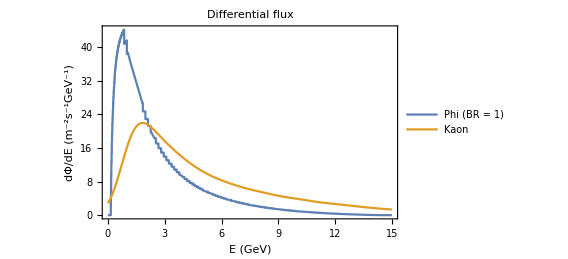

```mathematica
Plot[{PDF[totDist,x]*totFlux,dKFluxAll},{x,0,15},Frame->True,LabelStyle->{Black,15},ImageSize->420,FrameLabel->{"E (GeV)","dΦ/dE (m^-2s^-1GeV^-1)"},PlotLabel->"Differential flux",PlotLegends-> {"Phi (BR = 1)","Kaon"}]
```

Need to fix the artifacts present from the pdf stitching!

```mathematica
numPts =75;
distTable = Table[{If[i==-1, 0,If[i==0,mPhi,N[i*15/numPts]]],If[i==-1,0,If[i==0, 0,totFlux*PDF[totDist,N[(i*15/numPts)]]]]},{i,-1,numPts}]
```

{{0,0},{0.15,0},{0.2,15.1125},{0.4,34.9474},{0.6,41.1556},{0.8,43.6716},{1.,41.5881},{1.2,36.1554},{1.4,33.7527},{1.6,28.9444},{1.8,26.7307},{2.,22.8779},{2.2,21.213},{2.4,18.3296},{2.6,17.0809},{2.8,15.9422},{3.,13.9484},{3.2,13.0732},{3.4,11.5265},{3.6,10.842},{3.8,9.62452},{4.,9.08244},{4.2,8.11192},{4.4,7.67658},{4.6,6.89103},{4.8,6.53583},{5.,6.20279},{5.2,5.59569},{5.4,5.31834},{5.6,4.80917},{5.8,4.57517},{6.,4.14392},{6.2,3.94511},{6.4,3.57744},{6.6,3.40717},{6.8,3.09053},{7.,2.94309},{7.2,2.66794},{7.4,2.53969},{7.6,2.41734},{7.8,2.18952},{8.,2.08354},{8.2,1.88592},{8.4,1.79362},{8.6,1.62053},{8.8,1.5392},{9.,1.38602},{9.2,1.31394},{9.4,1.17855},{9.6,1.11519},{9.8,0.996842},{10.,0.941606},{10.2,0.838163},{10.4,0.789604},{10.6,0.742948},{10.8,0.654915},{11.,0.613393},{11.2,0.535126},{11.4,0.498329},{11.6,0.429283},{11.8,0.396979},{12.,0.336622},{12.2,0.308486},{12.4,0.256065},{12.6,0.231678},{12.8,0.186262},{13.,0.165115},{13.2,0.144932},{13.4,0.107277},{13.6,0.0897314},{13.8,0.0570345},{14.,0.0418043},{14.2,0.0133379},{14.4,0.},{14.6,0.},{14.8,0.},{15.,0.}}

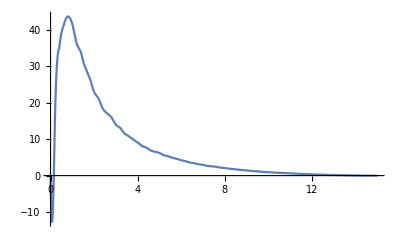

```mathematica
intDistTable=Interpolation[distTable,InterpolationOrder->3];
Plot[intDistTable[x],{x,0,15}]
```

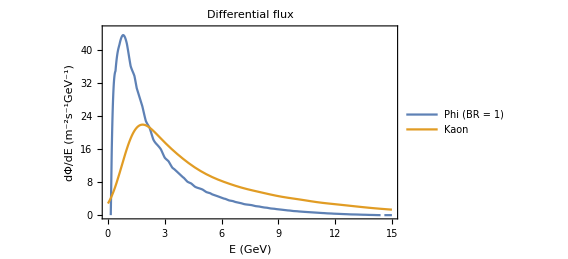

```mathematica
Plot[{intDistTable[x],dKFluxAll},{x,0,15},Frame->True,LabelStyle->{Black,15},ImageSize->420,PlotRange -> {0,45},FrameLabel->{"E (GeV)","dΦ/dE (m^-2s^-1GeV^-1)"},PlotLabel->"Differential flux",PlotLegends-> {"Phi (BR = 1)","Kaon"}]
```

### Theta Distribution

```mathematica
G2[R_,h_,θ_]:=N[Evaluate[Sin[θ]*((R+h)/L[θ,R,h])(1+((R*Cos[θ])/(L[θ,R,h]-R*Cos[θ])))]]
```

```mathematica
thetaDist[R_,h_,θ_,mPhi_]:=Sum[engStep*G2[R,h,θ]*Exp[-(L[θ,R,h]*1000)/(disTravel[minPhiEng + i*engStep,mPhi])]*PDF[totDist,minPhiEng+i*engStep]/disTravel[minPhiEng+i*engStep,mPhi],{i,1,149}]
```

```mathematica
thetaDist[6400,10,Pi/2.5,mPhi]
```

9.65941×10^-11

```mathematica
thetaNormalization = Sum[(Pi/100)*thetaDist[6400,10,i*Pi/100,mPhi],{i,1,100}]
```

General::munfl: Exp[-987.35] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.00314262 6.01354×10^-306 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-985.89] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

0.0000186049

General::munfl: Exp[-987.837] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 6.41783×10^-6 4.27603×10^-306 is too small to represent as a normalized machine number; precision may be lost.

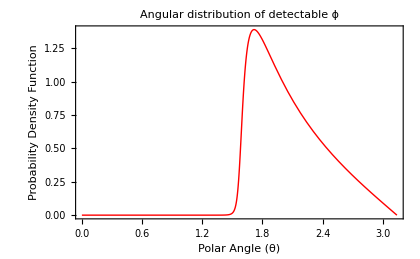

```mathematica
Plot[thetaDist[6400,10,θ,mPhi]/thetaNormalization,{θ,0,Pi},Frame->True,LabelStyle->{Black,15},ImageSize->420,FrameLabel->{"Polar Angle (θ)","Probability Density Function"},PlotLabel->"Angular distribution of detectable ϕ",PlotStyle->Directive[Red,Thick]]
```

### Opening Angle

```mathematica
pe[mPhi_] := me Sqrt[1-(2*me/mPhi)^2]
```

```mathematica
Ee[mPhi_] :=Sqrt[pe[mPhi]^2 + me^2]
```

```mathematica
OpeningAngle[phiEng_,mPhi_] := 2*ArcTan[pe[mPhi]*c/(velPhi[phiEng,mPhi]*gamma[phiEng,mPhi]*Ee[mPhi])]*180/Pi
```

```mathematica
OADistNorm[mPhi_]:=Sum[engStep*Gmod[6400,10,minPhiEng + i*engStep,mPhi]*PDF[totDist,minPhiEng+i*engStep]/disTravel[minPhiEng+i*engStep,mPhi],{i,1,149}]
```

```mathematica
OADNorm =OADistNorm[0.150]
```

0.0000186059

```mathematica
OADistList[mPhi_] := Table[{If[i==0, 46,OpeningAngle[minPhiEng+i*engStep,mPhi]],If[i==0,0,engStep*Gmod[6400,10,minPhiEng + i*engStep,mPhi]*PDF[totDist,minPhiEng+i*engStep]/disTravel[minPhiEng+i*engStep,mPhi]/OADNorm]},{i,0,149}]
```

```mathematica
OADistList[0.150]
```

{{46,0},{44.4148,0.0334481},{31.9248,0.045665},{25.074,0.0514003},{20.6933,0.0537687},{17.6354,0.0541635},{15.3741,0.053943},{13.6315,0.0490928},{12.2464,0.0480854},{11.1184,0.0434368},{10.1816,0.0391392},{9.39111,0.0351844},{8.71494,0.0343111},{8.1299,0.0308297},{7.61869,0.0277311},{7.16812,0.026959},{6.76798,0.0242256},{6.41024,0.0218108},{6.08849,0.0196799},{5.79755,0.019196},{5.53319,0.0173743},{5.29191,0.0157628},{5.07083,0.0143345},{4.8675,0.0140205},{4.67986,0.0127869},{4.50617,0.0116869},{4.34492,0.0114507},{4.19482,0.0104923},{4.05476,0.00963234},{3.92375,0.00885864},{3.80095,0.00869637},{3.68561,0.00801483},{3.57707,0.00739852},{3.47474,0.00684013},{3.3781,0.00672562},{3.2867,0.00622954},{3.20012,0.00577828},{3.11798,0.00568743},{3.03996,0.00528438},{2.96575,0.00491629},{2.89507,0.00457947},{2.82769,0.00451286},{2.76337,0.00420969},{2.70192,0.0039311},{2.64314,0.0036746},{2.58686,0.00362487},{2.53293,0.00339229},{2.48121,0.00317733},{2.43156,0.00313646},{2.38385,0.0029406},{2.33798,0.00275888},{2.29384,0.00259},{2.25134,0.00255874},{2.21039,0.00240388},{2.1709,0.00225951},{2.1328,0.00212478},{2.09601,0.00210063},{2.06047,0.00197655},{2.02611,0.00186053},{1.99288,0.00175198},{1.96073,0.00173316},{1.92959,0.00163282},{1.89943,0.00153873},{1.8702,0.00152285},{1.84185,0.0014356},{1.81435,0.00135355},{1.78766,0.0012763},{1.76175,0.00126378},{1.73657,0.00119184},{1.7121,0.00112398},{1.68832,0.00105997},{1.66518,0.00105007},{1.64267,0.000990366},{1.62077,0.000934057},{1.59944,0.000925634},{1.57866,0.000873116},{1.55841,0.0008236},{1.53868,0.000776902},{1.51944,0.000770202},{1.50068,0.00072658},{1.48238,0.000685367},{1.46451,0.000646383},{1.44707,0.000641041},{1.43005,0.000604473},{1.41341,0.00056979},{1.39716,0.000536859},{1.38128,0.0005326},{1.36576,0.000501598},{1.35058,0.000472129},{1.33574,0.000468493},{1.32122,0.00044074},{1.30701,0.000414389},{1.2931,0.000389401},{1.27949,0.000386514},{1.26616,0.000363048},{1.2531,0.000340842},{1.24031,0.000319835},{1.22778,0.000317549},{1.2155,0.000297828},{1.20347,0.000279143},{1.19167,0.000261415},{1.1801,0.000259611},{1.16875,0.000242897},{1.15761,0.000226995},{1.14669,0.000225468},{1.13597,0.000210438},{1.12545,0.00019612},{1.11513,0.000182481},{1.10499,0.000181294},{1.09503,0.000168401},{1.08525,0.000156134},{1.07565,0.000144474},{1.06621,0.000143563},{1.05694,0.000132568},{1.04783,0.000122136},{1.03887,0.000121384},{1.03007,0.000111564},{1.02141,0.000102263},{1.0129,0.0000934621},{1.00452,0.0000929038},{0.99629,0.0000846339},{0.98819,0.0000768166},{0.98022,0.0000694306},{0.972377,0.0000690278},{0.964659,0.0000620939},{0.957063,0.0000555437},{0.949585,0.0000493543},{0.942223,0.0000490761},{0.934975,0.0000432607},{0.927837,0.0000377616},{0.920807,0.0000375531},{0.913883,0.0000323826},{0.907062,0.0000274934},{0.900343,0.0000228722},{0.893722,0.0000227493},{0.887198,0.0000184076},{0.880769,0.0000143063},{0.874432,0.0000104307},{0.868185,0.0000103761},{0.862027,6.73002×10^-6},{0.855956,3.27633×10^-6},{0.84997,3.2595×10^-6},{0.844067,0.},{0.838246,0.},{0.832504,0.},{0.82684,0.},{0.821253,0.},{0.815741,0.},{0.810302,0.},{0.804936,0.}}

```mathematica
intOA=Interpolation[OADistList[mPhi],InterpolationOrder->1]
```

InterpolatingFunction[…]

InterpolatingFunction::dmval: Input value {0.00102143} lies outside the range of data in the interpolating function. Extrapolation will be used.

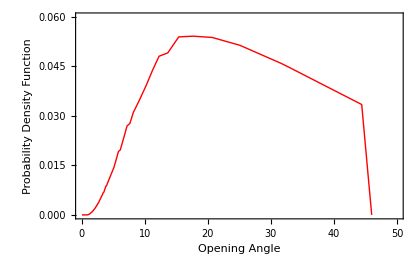

```mathematica
Plot[intOA[ang],{ang,0,50},FrameLabel->{"Opening Angle","Probability Density Function"},PlotRange -> {0,0.06},Frame->True,LabelStyle->{Black,15},ImageSize->420,PlotStyle->Directive[Red,Thick]]
```